## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
results={};
n=12;
primes=nprimes[n][[;;10000]];
```

## Prime 12

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv12=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv12];
```

```mathematica
count = Total[adj]//Counts
```

<|3→1863,5→1329,8→451,9→358,39→5,17→73,2→1241,7→624,4→1673,12→185,10→296,25→16,6→899,15→76,11→195,20→40,23→33,14→121,30→10,13→123,46→3,57→1,32→7,72→2,121→1,16→83,19→42,21→34,24→13,22→29,42→5,27→7,26→22,40→2,44→1,31→8,18→54,28→13,36→6,45→3,35→4,67→2,29→10,33→6,38→6,64→1,37→7,54→1,63→1,56→2,51→2,59→2,68→1,48→1,34→2,43→1,50→1,47→1,41→1|>

```mathematica
count[1]=.
```

```mathematica
count=Sort[count]
```

<|57→1,121→1,44→1,64→1,54→1,63→1,68→1,48→1,43→1,50→1,47→1,41→1,72→2,40→2,67→2,56→2,51→2,59→2,34→2,46→3,45→3,35→4,39→5,42→5,36→6,33→6,38→6,32→7,27→7,37→7,31→8,30→10,29→10,24→13,28→13,25→16,26→22,22→29,23→33,21→34,20→40,19→42,18→54,17→73,15→76,16→83,14→121,13→123,12→185,11→195,10→296,9→358,8→451,7→624,6→899,2→1241,5→1329,4→1673,3→1863|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{57,1/9999},{121,1/9999},{44,1/9999},{64,1/9999},{54,1/9999},{63,1/9999},{68,1/9999},{48,1/9999},{43,1/9999},{50,1/9999},{47,1/9999},{41,1/9999},{72,2/9999},{40,2/9999},{67,2/9999},{56,2/9999},{51,2/9999},{59,2/9999},{34,2/9999},{46,1/3333},{45,1/3333},{35,4/9999},{39,5/9999},{42,5/9999},{36,2/3333},{33,2/3333},{38,2/3333},{32,7/9999},{27,7/9999},{37,7/9999},{31,8/9999},{30,10/9999},{29,10/9999},{24,13/9999},{28,13/9999},{25,16/9999},{26,2/909},{22,29/9999},{23,1/303},{21,34/9999},{20,40/9999},{19,14/3333},{18,6/1111},{17,73/9999},{15,76/9999},{16,83/9999},{14,11/909},{13,41/3333},{12,185/9999},{11,65/3333},{10,296/9999},{9,358/9999},{8,41/909},{7,208/3333},{6,899/9999},{2,1241/9999},{5,443/3333},{4,1673/9999},{3,207/1111}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.419408/x^1.077]

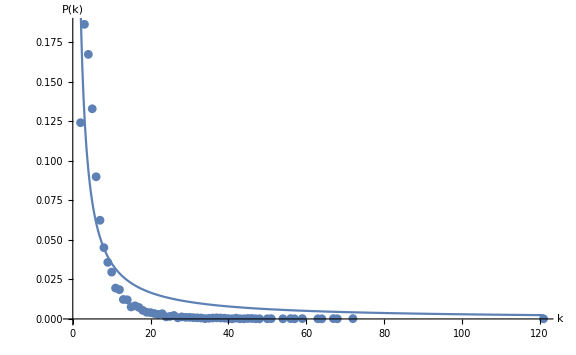

```mathematica
vis11=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv12]//Mean//N
```

6.30903

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh12=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh12];
```

```mathematica
count = Total[adj]//Counts
```

<|2→3723,3→2239,7→402,6→571,4→1431,9→150,8→268,12→44,11→62,5→920,10→112,15→15,20→3,18→5,14→16,13→24,16→8,21→3,17→1,19→2|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,1241/3333},{3,2239/9999},{7,134/3333},{6,571/9999},{4,159/1111},{9,50/3333},{8,268/9999},{12,4/909},{11,62/9999},{5,920/9999},{10,112/9999},{15,5/3333},{20,1/3333},{18,5/9999},{14,16/9999},{13,8/3333},{16,8/9999},{21,1/3333},{17,1/9999},{19,2/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.27275/x^1.71034]

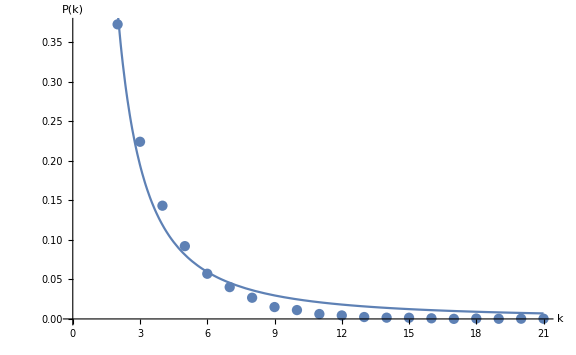

```mathematica
hvis11=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis12];
```

## Mean degree

```mathematica
degree=VertexDegree[igh12]//Mean//N
```

3.77118

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
diffs
```

{<|1→{13},121,384→{-4324306}|>,-14+1;;50000}
 |  |  |  |

```mathematica
results
```

{{horizontal,14,9999,3.77118,1.71034 ± 0.174246,1.27275 ± 0.215431},{visibility,14,9999,6.30903,1.077 ± 0.186338,0.419408 ± 0.113956}}